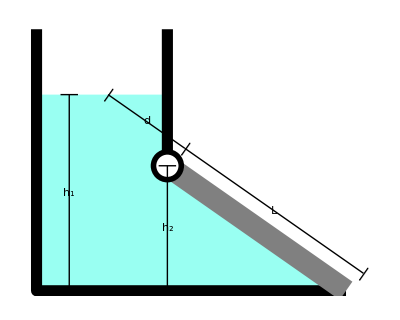

```mathematica
Module[{h,L,d,b,θ,w1,h1,w2,h2,δ1,δ2,col,gate,xgate},
h=2.25;L=2.5;d=h/Sin[θ]-L;b=1;(*m*)θ=35°;
w1=1.5;h1=d*Sin[θ];w2=L*Cos[θ];h2=L*Sin[θ];
δ1=0.1;δ2=0.2;col=RGBColor[0.6,1,0.95];

gate[x_]:=h2/(w1-(w1+w2))*(x-w1)+h2;
xgate=x/.Solve[gate[x]==h1+h2-δ2,x][[1]];

Graphics[{
{col,Polygon[{{0,h},{0,0},{w1+w2,0},{w1,h2},{w1,h}}]},

{Thickness@0.02,CapForm[None],Line[{{0,3},{0,0},{w1+w2,0}}],Line[{{w1,h2},{w1,3}}]},

{Thickness@0.04,CapForm["Round"],GrayLevel@0.5,Line[{{w1,h2},{w1+w2,0}}]},

{PointSize@0.06,Point@#,White,PointSize@0.04,Point@#}&@{w1,h2},

Line[{{0.25*w1,0},{0.25*w1,h}}],Line[{{0.25*w1+δ1,#},{0.25*w1-δ1,#}}]&/@{0,h},
Text[Framed[Style[Subscript[Style["h",Italic],1],17],Background->col,FrameStyle->None],{0.25*w1,h/2}],

Line[{{w1,0},{w1,h2}}],Line[{{w1+δ1,#},{w1-δ1,#}}]&/@{0,h2},
Text[Framed[Style[Subscript[Style["h",Italic],2],17],Background->col,FrameStyle->None],{w1,h2/2}],

Line[{{w1+δ2,h2+δ2},{w1+w2+δ2,δ2}}],
Text[Rotate[Style["—",17],90°-θ],#]&/@{{w1+δ2,h2+δ2},{w1+w2+δ2,δ2}},
Text[Framed[Style["L",Italic,17],Background->White,FrameStyle->None],{2*w1+w2+2*δ2,h2+2*δ2}/2],

Line[{{w1+δ2,h2+δ2},{xgate+δ2,gate[xgate]+δ2}}],
Text[Rotate[Style["—",17],90°-θ],{xgate+δ2,gate[xgate]+δ2}],
Text[Framed[Style["d",Italic,17],Background->col,FrameStyle->None],{w1+xgate+2*δ2,h2+gate[xgate]+2*δ2}/2]
}]
]
```